```mathematica
d=-0.12; mu2=0.225; t=0.4; c=6.25;a1=0.00125; G1=0.00086; b=0.00005138;
f5[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+4*U^2*d^2+2*t^2*d*U+t^4/4));
F3[x_,n1_,U_]=(1/((mu2-f5[x,n1,U])^2+G1^2));
f4[x_,U_]=b*0.5*G1*Sum[F3[x,n1,U],{n1,0,100}]*(1/x);
Plot[{f4[x,0.08],f4[x,0.1],f4[x,0.14]+2,f4[x,0.165]+4,2,4},{x,0,0.1},PlotRange->{0,6.5},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red,Dashed},{Thickness[0.003],Green},{Thickness[0.003],Blue},{Thickness[0.003],Black},{Thickness[0.003],Black}},FrameLabel->{Style["1/B, T^-1",10],Style["DOS, rel. units",10]},Epilog->{{Black,Text["U = 80   meV",{0.075,0.9},{-1,-1}]},{Black,Text["U = 100  meV",{0.075,1.3},{-1,-1}]},{Black,Text["U = 140  meV",{0.075,3.0},{-1,-1}]},{Black,Text["U = 165 meV",{0.075,5.0},{-1,-1}]}},Frame->True]
```

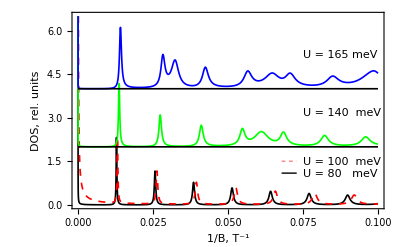

Graphics::gprim: -Dashing[{0, Small}] + Dashing[{Small, Small}] was encountered where a Graphics primitive or directive was expected.

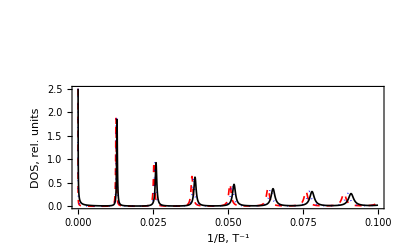

```mathematica
Plot[{f4[x,0.07],f4[x,0.08],f4[x,0.09]},{x,0,0.1},PlotRange->{0,2.5},PlotStyle->{{Thickness[0.003],Red, Dashed},{Thickness[0.003],Blue, Dotted},{Thickness[0.003],Dashed-Dotted,Black},{Thickness[0.003],Dashed,Black}},Epilog->{{Black,Text["U = 70  meV",{0.065,22},{-1,-1}]},{Black,Text["U = 80  meV",{0.065,20},{-1,-1}]},{Black,Text["U = 90 meV",{0.065,18},{-1,-1}]}},FrameLabel->{Style["1/B, T^-1",10],Style["DOS, rel. units",10]},Frame->True]
```